# X-ray emission from magnetars

## 1. Gaunt factors

```mathematica
hbar=1.0545718176461565*10^(-27);
e=4.803204712570263*10^(-10);
me=9.1093837015*10^(-28);
c=29979245800.0;
kb=1.380649*10^(-16);
kev2erg=1.6021766339999998*10^-9;
mp=1.67262192369*10^-24;
G=6.674299999999999*10^-8;
Ms=1.988409870698051*10^33;
```

### gaunt factors

```mathematica
C0[a_]:=N[1/a-Exp[a]*ExpIntegralE[1,a]]
C1[a_]:=N[(1+a)*Exp[a]*ExpIntegralE[1,a]-1]
(*计算guunt factor，其中r1是E/kT,r2是omega/omegac
*)
gl[r1_,r2_]:=NIntegrate[Exp[-r1*r2*Sinh[x]^2]*C1[r2*Exp[2 x]],{x,-Infinity,Infinity}]
gp[r1_,r2_]:=NIntegrate[Exp[-r1*r2*Sinh[x]^2]*2*r2*Exp[2x]C0[r2*Exp[2 x]],{x,-Infinity,Infinity}]
```

### Check gaunt factor with van Adelsberg & Lai 2006

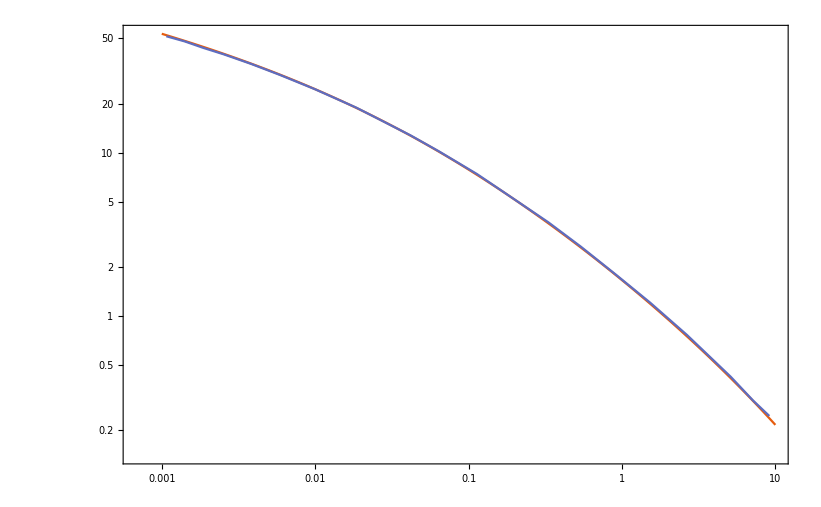

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
linearspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];
(*Ekev=Table[x,{x,0.001,10,0.001}];*)
Ekev=logspace[-3,1,100];
Ec=Ekev*kev2erg;
ω=Ec/hbar;
B=10^13;
ωc=e*B/me/c;
T=10^6;
r1=hbar*ωc/(kb*T);
r2=ω/ωc;
gaunt=gl[r1,r2];
data=Transpose@{Ekev,gaunt};
list=Import["/Users/yonggao/Desktop/magnetar_precession/code/gaunt.csv"];
ListLogLogPlot[{data,list},PlotRange->All,Joined->True,PlotTheme->"Scientific",Background->White]
```

## Calculate the opacity

### method1

```mathematica
dielectric[B_,Es_,ρ_,T_,θb_]:=Module[{ue,ui,ve,vi,γre,γri,r1,r2,γeiL,γeip,ϵpla,ηpla,ϵ,η,g},
Z=1;A=1;Ye=Z/A;
Ec=Es*kev2erg;
ωc=(e B)/(me c);
ue=((hbar*ωc)/Ec)^2;
ui=((hbar*ωc)/Ec*me/mp)^2;
ve=((hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5)/Ec)^2;
vi=((Z me)/(A mp))*ve;
γre=9.52*10^-6 Ec/(1*kev2erg);
γri=5.2*10^-9 Z^2/A*Ec/(1*kev2erg);
r1=hbar*ωc/(kb*T);
r2=Ec/hbar/ωc;
γeiL=9.24*10^-5*(Z^2*(ρ/1))/(A (T/10^6)^0.5(Ec/kev2erg)^2)*(1-Exp[-Ec/(kb*T)])*gl[r1,r2];
γeip=9.24*10^-5*(Z^2*(ρ/1))/(A (T/10^6)^0.5(Ec/kev2erg)^2)(1-Exp[-Ec/(kb*T)])*gp[r1,r2];
ϵpg=1-(ve(1+I * γri)+vi (1+I *γre))/((1+I* γre + ue^0.5)*(1+I* γri-ui^0.5)+I *γeiL);
ϵmg=1-(ve(1+I * γri)+vi (1+I* γre))/((1+I* γre - ue^0.5)*(1+I *γri+ui^0.5)+I* γeiL);
ϵpla=(ϵpg+ϵmg)/2;
g=(ϵpg-ϵmg)/2;
ηpla=1-ve/(1+I * (γeip+γre))-vi/(1+ I *(γeip+γri));
(*M=(A mp)/(Z me);
ϵpla=1-(ve(1-M ui))/((1-ui)(1-ue));
ηpla=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));*)

αF=e^2/hbar/c;
BQ=me^2*c^3/e/hbar;
b=B/BQ;
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
ϵ=ϵpla+a-1;
η=ηpla+a+q-1;
r=1+m/a Sin[θb]^2;
β=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θb]^2/Cos[θb];
K1=β(1+(-1)^1(1+r/β^2)^(1/2));
K2=β(1+(-1)^2(1+r/β^2)^(1/2));
Kz1=-(((ϵpla-ηpla-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb])/(ϵpla*Sin[θb]^2+(ηpla+q)Cos[θb]^2+a-1));

Kz2=-(((ϵpla-ηpla-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb])/(ϵpla*Sin[θb]^2+(ηpla+q)Cos[θb]^2+a-1));
ep2=Abs[1+K1*Cos[θb]+Kz1*Sin[θb]]^2/(2(1+Abs[K1]^2+Abs[Kz1]^2));
ep22=Abs[1+K2*Cos[θb]+Kz2*Sin[θb]]^2/(2(1+Abs[K2]^2+Abs[Kz2]^2));
em2=Abs[1-(K1*Cos[θb]+Kz1*Sin[θb])]^2/(2(1+Abs[K1]^2+Abs[Kz1]^2));
em22=Abs[1-(K2*Cos[θb]+Kz2*Sin[θb])]^2/(2(1+Abs[K2]^2+Abs[Kz2]^2));
e02=Abs[K1 * Sin[θb]-Kz1*Cos[θb]]^2/(1+Abs[K1]^2+Abs[Kz1]^2);
e022=Abs[K2 * Sin[θb]-Kz2*Cos[θb]]^2/(1+Abs[K2]^2+Abs[Kz2]^2);
γp=γeiL+(1+ue^0.5)γre+(1-ui^0.5)γri;

γm=γeiL+(1-ue^0.5)γre+(1+ui^0.5)γri;
Λp=((1+ue^0.5)^2(1-ui^0.5)^2+γp^2)^-1;
Λm=((1-ue^0.5)^2(1+ui^0.5)^2+γm^2)^-1;
κp=Ec/(hbar c ρ)ve Λp γeiL;
κm=Ec/(hbar c ρ)ve Λm γeiL;
κo=Ec/(hbar c ρ)ve γeip;

κff1=κp*ep2 + κm*em2 + κo*e02;
κff2=κp*ep22 + κm*em22 + κo*e022;
{N[κff1],N[κff2]}]
```

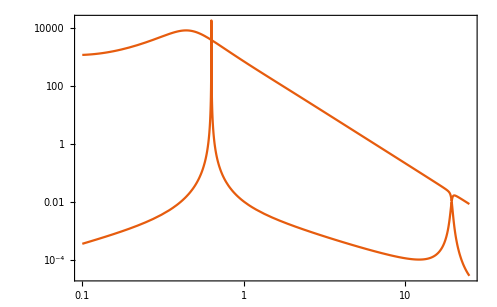

```mathematica
B=10^14;ρ=5.4;T=10^6;θb=π/4;
LogLogPlot[dielectric[B,Es,ρ,T,θb],{Es,0.1,25},PlotRange->Full,PlotTheme->"Scientific"]
```

### method2

```mathematica
C0[a_]:=N[1/a-Exp[a]*ExpIntegralE[1,a]]
C1[a_]:=N[(1+a)*Exp[a]*ExpIntegralE[1,a]-1]
(*计算guunt factor，其中r1是E/kT,r2是omega/omegac
*)
gl[r1_,r2_]:=NIntegrate[Exp[-r1*r2*Sinh[x]^2]*C1[r2*Exp[2 x]],{x,-Infinity,Infinity}]
gp[r1_,r2_]:=NIntegrate[Exp[-r1*r2*Sinh[x]^2]*2*r2*Exp[2x]C0[r2*Exp[2 x]],{x,-Infinity,Infinity}]
dielectric[B_,Es_,ρ_,T_,θb_]:=Module[{ue,ui,ve,M,ϵpla,ηpla,ϵ,η,g},
Z=1;A=1;Ye=Z/A;
M=(A mp)/(Z me);
Ec=Es*kev2erg;
ωc=(e B)/(me c);
ue=((hbar*ωc)/Ec)^2;
ui=((hbar*ωc)/Ec*me/mp)^2;
ve=((hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5)/Ec)^2;
ϵpla=1-(ve(1-M ui))/((1-ui)(1-ue));
ηpla=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
αF=e^2/hbar/c;
BQ=me^2*c^3/e/hbar;
b=B/BQ;
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
ϵ=ϵpla+a-1;
η=ηpla+a+q-1;
r=1+m/a Sin[θb]^2;
β=-(ϵ^2-g^2-ϵ *η(1+m/a))/(2g η)Sin[θb]^2/Cos[θb];
K1=β(1+(-1)^1(1+r/β^2)^(1/2));
Kz1=-((ϵpla-ηpla-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb])/(ϵpla*Sin[θb]^2+(ηpla+q)Cos[θb]^2+a-1);

ep1=(1+(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
em1=(1-(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
e01=(K1 * Sin[θb]-Kz1*Cos[θb])^2/(1+K1^2+Kz1^2);

K2=β(1+(-1)^2(1+r/β^2)^(1/2));
Kz2=-((ϵpla-ηpla-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb])/(ϵpla*Sin[θb]^2+(ηpla+q)Cos[θb]^2+a-1);

ep2=(1+(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
em2=(1-(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
e02=(K2 * Sin[θb]-Kz2*Cos[θb])^2/(1+K2^2+Kz2^2);
ni=ρ/mp;
ne=ρ/mp * Z/A;
ω=Ec/hbar;
α0=4*π^2*Z^2*αF^3*(hbar^2 c^2)/me^2((2 me)/(π*kb*T))^0.5(ne*ni)/ω^3*(1-Exp[-Ec/(kb*T)]);
r1=hbar*ωc/(kb*T);
r2=Ec/hbar/ωc;
σT=8*π/3 * e^4/(c^4 me^2);
L=gl[r1,r2];
P=gp[r1,r2];
νre=(2 e^2 ω^2)/(3 me c^3);
νcep=(α0*L)/(ne σT)νre;
νcem=(α0*L)/(ne σT)νre;
νce0=(α0*P)/(ne σT)νre;
νri=(Z^2 me)/(A mp)νre;
νcip=me/(A mp)νcep;
νcim=me/(A mp)νcem;
νci0=me/(A mp)νce0;
κe1=α0/ρ(ω^2/((ω+ωc)^2+(νre+νcep)^2)L*ep1+ω^2/(ω^2+(νre+νce0)^2)P*e01+
ω^2/((ω-ωc)^2+(νre+νcem)^2)L*em1);
κi1=(ω^2/((ω-ωc)^2+(νri+νcip)^2)L*ep1+ω^2/((ω)^2+(νri+νci0)^2)P*e01+ω^2/((ω+ωc)^2+(νri+νcim)^2)L*em1)α0/ρ*1/Z^3((Z^2 me)/(A mp))^2;

κe2=α0/ρ(ω^2/((ω+ωc)^2+(νre+νcep)^2)L*ep2+ω^2/(ω^2+(νre+νce0)^2)P*e02+
ω^2/((ω-ωc)^2+(νre+νcem)^2)L*em2);
κi2=(ω^2/((ω-ωc)^2+(νri+νcip)^2)L*ep2+ω^2/((ω)^2+(νri+νci0)^2)P*e02+ω^2/((ω+ωc)^2+(νri+νcim)^2)L*em2)α0/ρ*1/Z^3((Z^2 me)/(A mp))^2;
κff1=κe1+κi1;
κff2=κe2+κi2;
κes1=(ne*σT)/ρ*(ω^2/((ω+ωc)^2+(νre+νcep)^2)*ep1+ω^2/(ω^2+(νre+νce0)^2)*e01+
ω^2/((ω-ωc)^2+(νre+νcem)^2)*em1);
κes2=(ne*σT)/ρ*(ω^2/((ω+ωc)^2+(νre+νcep)^2)*ep2+ω^2/(ω^2+(νre+νce0)^2)*e02+
ω^2/((ω-ωc)^2+(νre+νcem)^2)*em2);

κis1=((Z^2 me)/(A mp))^2(ne*σT)/ρ*(ω^2/((ω-ωc)^2+(νri+νcip)^2)*ep1+ω^2/(ω^2+(νri+νci0)^2)*e01+
ω^2/((ω+ωc)^2+(νri+νcim)^2)*em1);

κis2=((Z^2 me)/(A mp))^2(ne*σT)/ρ*(ω^2/((ω-ωc)^2+(νri+νcip)^2)*ep2+ω^2/(ω^2+(νri+νci0)^2)*e02+
ω^2/((ω+ωc)^2+(νri+νcim)^2)*em2);
κs1=κes1+κis1;
κs2=κes2+κis2;

{κff1}]
```

```mathematica
dielectric1[B_,Es_,ρ_,T_,θb_]:=Module[{ue,ui,ve,M,ϵpla,ηpla,ϵ,η,g},
Z=1;A=1;Ye=Z/A;
M=(A mp)/(Z me);
Ec=Es*kev2erg;
ωc=(e B)/(me c);
ue=((hbar*ωc)/Ec)^2;
ui=((hbar*ωc)/Ec*me/mp)^2;
ve=((hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5)/Ec)^2;
ϵpla=1-(ve(1-M ui))/((1-ui)(1-ue));
ηpla=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
αF=e^2/hbar/c;
BQ=me^2*c^3/e/hbar;
b=B/BQ;
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
ϵ=ϵpla+a-1;
η=ηpla+a+q-1;
r=1+m/a Sin[θb]^2;
β=-(ϵ^2-g^2-ϵ *η(1+m/a))/(2g η)Sin[θb]^2/Cos[θb];
K1=β(1+(-1)^1(1+r/β^2)^(1/2));
Kz1=-((ϵpla-ηpla-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb])/(ϵpla*Sin[θb]^2+(ηpla+q)Cos[θb]^2+a-1);

ep1=(1+(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
em1=(1-(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
e01=(K1 * Sin[θb]-Kz1*Cos[θb])^2/(1+K1^2+Kz1^2);

K2=β(1+(-1)^2(1+r/β^2)^(1/2));
Kz2=-((ϵpla-ηpla-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb])/(ϵpla*Sin[θb]^2+(ηpla+q)Cos[θb]^2+a-1);

ep2=(1+(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
em2=(1-(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
e02=(K2 * Sin[θb]-Kz2*Cos[θb])^2/(1+K2^2+Kz2^2);
ni=ρ/mp;
ne=ρ/mp * Z/A;
ω=Ec/hbar;
α0=4*π^2*Z^2*αF^3*(hbar^2 c^2)/me^2((2 me)/(π*kb*T))^0.5(ne*ni)/ω^3*(1-Exp[-Ec/(kb*T)]);
r1=hbar*ωc/(kb*T);
r2=Ec/hbar/ωc;
σT=8*π/3 * e^4/(c^4 me^2);
L=gl[r1,r2];
P=gp[r1,r2];
νre=(2 e^2 ω^2)/(3 me c^3);
νcep=(α0*L)/(ne σT)νre;
νcem=(α0*L)/(ne σT)νre;
νce0=(α0*P)/(ne σT)νre;
νri=(Z^2 me)/(A mp)νre;
νcip=me/(A mp)νcep;
νcim=me/(A mp)νcem;
νci0=me/(A mp)νce0;
κe1=α0/ρ(ω^2/((ω+ωc)^2+(νre+νcep)^2)L*ep1+ω^2/(ω^2+(νre+νce0)^2)P*e01+
ω^2/((ω-ωc)^2+(νre+νcem)^2)L*em1);
κi1=(ω^2/((ω-ωc)^2+(νri+νcip)^2)L*ep1+ω^2/((ω)^2+(νri+νci0)^2)P*e01+ω^2/((ω+ωc)^2+(νri+νcim)^2)L*em1)α0/ρ*1/Z^3((Z^2 me)/(A mp))^2;

κe2=α0/ρ(ω^2/((ω+ωc)^2+(νre+νcep)^2)L*ep2+ω^2/(ω^2+(νre+νce0)^2)P*e02+
ω^2/((ω-ωc)^2+(νre+νcem)^2)L*em2);
κi2=(ω^2/((ω-ωc)^2+(νri+νcip)^2)L*ep2+ω^2/((ω)^2+(νri+νci0)^2)P*e02+ω^2/((ω+ωc)^2+(νri+νcim)^2)L*em2)α0/ρ*1/Z^3((Z^2 me)/(A mp))^2;
κff1=κe1+κi1;
κff2=κe2+κi2;
κes1=(ne*σT)/ρ*(ω^2/((ω+ωc)^2+(νre+νcep)^2)*ep1+ω^2/(ω^2+(νre+νce0)^2)*e01+
ω^2/((ω-ωc)^2+(νre+νcem)^2)*em1);
κes2=(ne*σT)/ρ*(ω^2/((ω+ωc)^2+(νre+νcep)^2)*ep2+ω^2/(ω^2+(νre+νce0)^2)*e02+
ω^2/((ω-ωc)^2+(νre+νcem)^2)*em2);

κis1=((Z^2 me)/(A mp))^2(ne*σT)/ρ*(ω^2/((ω-ωc)^2+(νri+νcip)^2)*ep1+ω^2/(ω^2+(νri+νci0)^2)*e01+
ω^2/((ω+ωc)^2+(νri+νcim)^2)*em1);

κis2=((Z^2 me)/(A mp))^2(ne*σT)/ρ*(ω^2/((ω-ωc)^2+(νri+νcip)^2)*ep2+ω^2/(ω^2+(νri+νci0)^2)*e02+
ω^2/((ω+ωc)^2+(νri+νcim)^2)*em2);
κs1=κes1+κis1;
κs2=κes2+κis2;

{κff2}]
```

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
linearspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];
Es=logspace[0.1,10,100];
B=10^14;ρ=1;T=10^6;θb=π/4;
κ1=dielectric[B,Es,ρ,T,θb];
(*data=Transpose@{Es,κ1};
*)
(*Export["/Users/yonggao/Desktop/Recent_project/magnetar_precession/code/kappa1.txt",data]*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

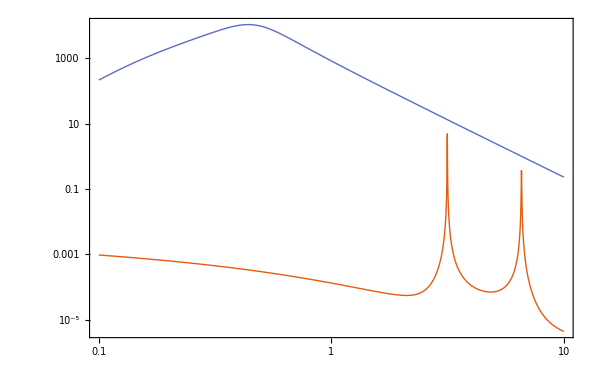

```mathematica
B=5*10^14;ρ=370;T=5*10^6;θb=π/4;
LogLogPlot[{dielectric[B,Es,ρ,T,θb],dielectric1[B,Es,ρ,T,θb]},{Es,0.1,10},PlotRange->Full,PlotTheme->"Scientific",Background->White,ImageSize->{360,222},AspectRatio->Full,PlotStyle-> Thick,FrameTicksStyle->Directive[{Black,25}]]
```



```mathematica
Plot[Sin[x],{x,0,10},TicksStyle->Directive[Orange,25]]
```

```mathematica
Rasterize[%136,"Image"]
```

-Graphics-

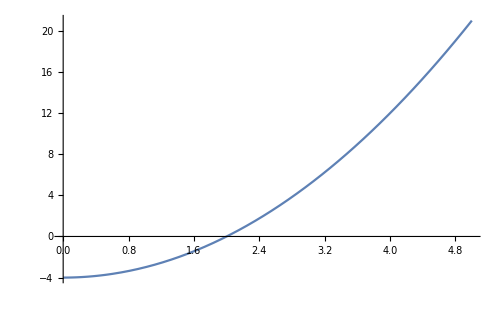
-Graphics-Y axisX Axis

```mathematica
Labeled[Plot[x^2-4,{x,0,5},ImageSize->500,AxesOrigin->{0,0}],{"Y axis","X Axis"},{Left,Bottom},RotateLabel->True]
```

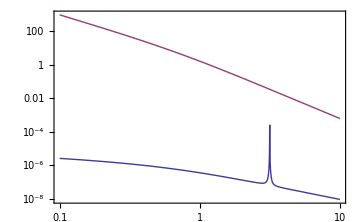

```mathematica
Show[%120,ImageSize->{360,222},AspectRatio->Full]
```

## Resonance of the photons

```mathematica
Ead[B_,T_,θb_]:=Module[{q,m,αF,ωc,Ebi,M,R},
Z=1;
A=1;
Ye=Z/A;
αF=e^2/hbar/c;
BQ=me^2*c^3/e/hbar;
b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
fB=((3*δv)/(q+m))^0.5;
M=1.4*Ms;
R=10^6;
g=(G*M)/R^2(1-(2G M)/(R c^2))^(-1/2);
Hρ=2*kb*T/(mp * g *Cos[θb]);
ωc=(e B)/(me c);
Ebi=hbar*ωc*me/mp/kev2erg;
(*adiabatic=2.52*(fB*Tan[θb])^(2/3)*(Abs[1-(Ebi/Es)^2])^(2/3)*(1/(.7fHρ))^(1/3);*)
solution=NSolve[Es-2.52*(fB*Tan[θb])^(2/3)*(Abs[1-(Ebi/Es)^2])^(2/3)(1/Hρ)^(1/3)==0,Es];
solution
]
```

## Temperature profile

```mathematica
(*T=5*10^6, B=5*10^14*)
temperature[τ_]:=Module[{τmid,x,tem},
τmid=63.2;
a1=0.761;
a2= 0.00198;
a3=0.267;
a4=−0.356;
a5= 0.179;
a6=−0.0282;
b3=−0.118;
b4=−0.0336;
b5=−0.00428;
b6=−0.00022;
x=Log[10,τ]-Log[10,τmid];
Which[τ>τmid && τ≤2*10^4,tem=10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5),τ≤ τmid && τ≥ 10^-3,tem=10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)];
tem]
```

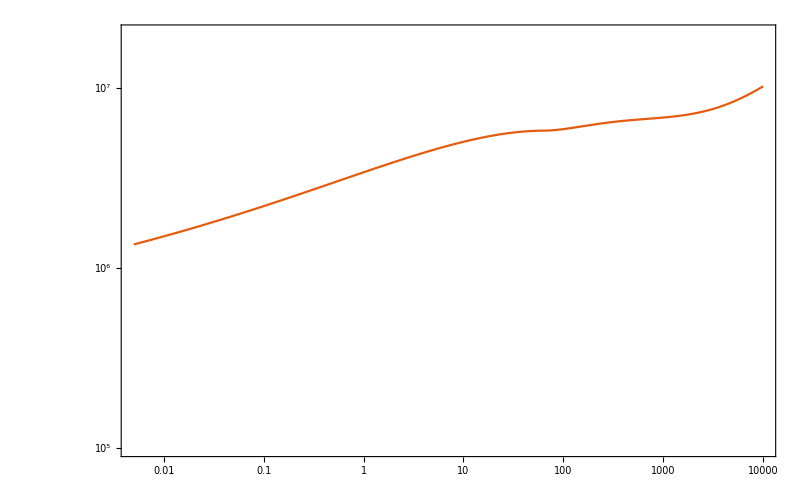

```mathematica
LogLogPlot[temperature[τ],{τ,0.005,10000},PlotTheme->"Scientific",PlotRange-> {{0.005,10000},{0.1*10^6,20*10^6}},Background->White,FrameTicksStyle->Directive[{Black,25}]]
```

## Adiabatic energy and jump probability

```mathematica
(*Upward integration*)
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
linearspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];
Pjump[Es_,B_,θb_]:=Module[{q,m,αF,ωc,Ebi,M,R,Ead},
Z=1;
A=1;
Ye=Z/A;
αF=e^2/hbar/c;
BQ=me^2*c^3/e/hbar;
b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
fB=((3*δv)/(q+m))^0.5;
M=1.4*Ms;
R=10^6;
g=(G*M)/R^2(1-(2G M)/(R c^2))^(-1/2);
ωc=(e B)/(me c);
Ebi=hbar*ωc*me/mp/kev2erg;
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
κT=0.4;
(*cons=(mp g)/(κT 2 ρv kb);*)
τv=11.85783;
Tv=temperature[τv];
Hρ=2*kb*Tv/(mp * g *Cos[θb]);
Ead=2.52*(fB*Tan[θb])^(2/3)*(Abs[1-(Ebi/Es)^2])^(2/3)(1/Hρ)^(1/3);
jump=Exp[-π/2(Es/Ead)^3];
N[jump]
]
```

## Radiative transfer equation

```mathematica
Sign
```

NIntegrate::inumri: The integrand ⅇ^(-2.3209 x Sinh[x]^2) (-1.+2.71828^(0.00017276 2.71828^(2. x) x) (1.+0.00017276 2.71828^(2. x) x) ExpIntegralE[1.,0.00017276 2.71828^(2. x) x]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-42.4925}}.

NIntegrate::inumri: The integrand 0.00034552 ⅇ^(2 x-2.3209 x («1»)^2) x ((5788.38 2.71828^(-2. x))/x-1. 2.71828^(0.00017276 2.71828^(2. x) x) ExpIntegralE[1.,0.00017276 2.71828^(2. x) x]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-42.4925}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand ⅇ^(-2.3209 x Sinh[x]^2) (-1.+2.71828^(0.00017276 2.71828^(2. x) x) (1.+0.00017276 2.71828^(2. x) x) ExpIntegralE[1.,0.00017276 2.71828^(2. x) x]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-42.4925}}.

NIntegrate::inumri: The integrand 0.00034552 ⅇ^(2 x-2.3209 x («1»)^2) x ((5788.38 2.71828^(-2. x))/x-1. 2.71828^(0.00017276 2.71828^(2. x) x) ExpIntegralE[1.,0.00017276 2.71828^(2. x) x]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-42.4925}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand ⅇ^(-2.3209 x Sinh[x]^2) (-1.+2.71828^(0.00017276 2.71828^(2. x) x) (1.+0.00017276 2.71828^(2. x) x) ExpIntegralE[1.,0.00017276 2.71828^(2. x) x]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-42.4925}}.

NIntegrate::inumri: The integrand 0.00034552 ⅇ^(2 x-2.3209 x («1»)^2) x ((5788.38 2.71828^(-2. x))/x-1. 2.71828^(0.00017276 2.71828^(2. x) x) ExpIntegralE[1.,0.00017276 2.71828^(2. x) x]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-42.4925}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand ⅇ^(-2.3209 x Sinh[x]^2) (-1.+2.71828^(0.00017276 2.71828^(2. x) x) (1.+0.00017276 2.71828^(2. x) x) ExpIntegralE[1.,0.00017276 2.71828^(2. x) x]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-42.4925}}.

NIntegrate::inumri: The integrand 0.00034552 ⅇ^(2 x-2.3209 x («1»)^2) x ((5788.38 2.71828^(-2. x))/x-1. 2.71828^(0.00017276 2.71828^(2. x) x) ExpIntegralE[1.,0.00017276 2.71828^(2. x) x]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-42.4925}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.